```mathematica
Clear[interPP,isumPP ,isumZP,isumZZ,isumWW,isumWWdyt]
SetDirectory[NotebookDirectory[]];
interPP = Get["intang_PPtt_3TeV_fix.txt"];
interZP = Get["intang_ZPtt_3TeV_fix.txt"];
```

```mathematica
interWW = Get["intang_WWtt1_3TeV.txt"];
interZZ = Get["intang_ZZtt_3TeV_Fix.txt"];
```

```mathematica
dytinterWW = Get["intang_WWttDYT_3TeV_2dyt.txt"];
dytinterWWex = Get["intang_WWttDYT_3TeV_20_new.txt"];
dytinterWW11= Get["intang_WWttDYT11_3TeV_2dyt.txt"];
dytinterWWm1m1= Get["intang_WWttDYTm1m1_3TeV_2dyt.txt"];
dytinterWW11ex= Get["intang_WWttDYT11_3TeV_dyt.txt"];
dytinterWWm1m1ex= Get["intang_WWttDYTm1m1_3TeV_dyt.txt"];
dytinterZZ = Get["intang_ZZtt00DYT_3TeV_20_new.txt"];
dytinterZZ11= Get["intang_ZZtt11DYT_3TeV_20.txt"];
dytinterZZm1m1= Get["intang_ZZttm1m1DYT_3TeV_20.txt"];
dytt = Table[(1/1000)*(20i-200),{i,0,20}]
```

{-1/5,-9/50,-4/25,-7/50,-3/25,-1/10,-2/25,-3/50,-1/25,-1/50,0,1/50,1/25,3/50,2/25,1/10,3/25,7/50,4/25,9/50,1/5}



```mathematica
(*benchmarklist={3,4,5,7,8,10,11};*)
ColorData[24,"Image"]
(*ColorData[109,"Image"]*)
colorselecitonumber=24;
```

```mathematica
energygrid=Grid[{Table[Style[If[j==1,{"(√s= 3,","6,","10,","14,","30,","100 TeV)"}[[i]],"TeV"],If[j≠0,ColorData[colorselecitonumber][i]],Bold],{j,1,2,1},{i,1,6,1}][[1]]},Spacings->{0.5,0}]
```

(√s= 3, | 6, | 10, | 14, | 30, | 100 TeV)

```mathematica
dytt[[11]]
```

0

```mathematica
angenPP[ang_,num_] :=interPP[[ang]] [(1 + ((num - 350)/50))]

angenZP[ang_,num_] :=interZP[[ang]] [(1 + ((num - 350)/50))]

angenWW[ang_,num_] :=interWW[[ang]][(1 + ((num - 350)/50))]

angenZZ[ang_,num_] :=interZZ[[ang]][(1 + ((num - 350)/50))]
```

```mathematica
isumWWdyt[ang_,dyt_,energy_] :=dytinterWW[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWW[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumWWdytex[ang_,dyt_,energy_] :=dytinterWWex[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWW[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumWWdyt11[ang_,dyt_,energy_] :=dytinterWW11[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWW11[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumWWdyt11ex[ang_,dyt_,energy_] :=dytinterWW11ex[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWW11[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumWWdytm1m1[ang_,dyt_,energy_] :=dytinterWWm1m1[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWWm1m1[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumWWdytm1m1ex[ang_,dyt_,energy_] :=dytinterWWm1m1ex[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWWm1m1[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumZZdyt00[ang_,dyt_,energy_] :=dytinterZZ[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZZ[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumZZdyt11[ang_,dyt_,energy_] :=dytinterZZ11[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZZ11[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumZZdytm1m1[ang_,dyt_,energy_] :=dytinterZZm1m1[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZZm1m1[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
lum = 1;
br = 72/81;
sqrtsbin = Table[350+50*i,{i,0,54}];
```

```mathematica
background = Table[NIntegrate[br*lum*(angenPP[k,ss]+angenWW[k,ss]+angenZP[k,ss]+angenZZ[k,ss]),{ss,sqrtsbin[[i]],sqrtsbin[[i+1]]}],{i,1,53},{k,1,18}];
```

```mathematica
isumWWdyt[1,12,400]
```

-0.00184346

```mathematica
isumWWdytex[1,12,400]*2
```

-0.00186856

```mathematica
isumWWdytm1m1ex[1,15,400]*2
```

0.000014636

```mathematica
isumWWdyt11[1,15,400]
```

0.0000177358

```mathematica
isumWWdytm1m1ex[1,15,400]*2
```

0.000014636

```mathematica
isumWWdytm1m1[1,15,400]
```

0.0000177358

```mathematica
(* ***Here remove isumZZdyt00, isumZZdyt11, isumZZdytm1m1 to get chi-square for only only WW. Remove the "ex" in isumWWdytex,isumWWdyt11ex,isumWWdytm1m1ex to get fit for the case when dyt for WW is twice as ZZ. This would be necessary to find the cubic coefficients in the kappa fit.*** *)
```

```mathematica
signal = Table[NIntegrate[br*lum*((isumWWdytex[k,j,ss]+isumWWdyt11ex[k,j,ss]+isumWWdytm1m1ex[k,j,ss])+ (1*(isumZZdyt00[k,j,ss]+isumZZdyt11[k,j,ss]+isumZZdytm1m1[k,j,ss]))),{ss,sqrtsbin[[i]],sqrtsbin[[i+1]]}],{i,1,53},{k,1,18},{j,1,Length@dytt}]
(*+isumZZdyt00[k,j,ss]+isumZZdyt11[k,j,ss]+isumZZdytm1m1[k,j,ss]*)
(*isumWWdyt[k,j,ss]+isumWWdyt11[k,j,ss]+isumWWdytm1m1[k,j,ss]*)
(*+(isumZZdyt00[k,j,ss]+isumZZdyt11[k,j,ss]+isumZZdytm1m1[k,j,ss])*)
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
(*Sum angles*)
sumanglesbkg = Table[Sum[background[[i,n]],{n,2,17}],{i,1,53}];
sumanglessig = Table[Sum[signal[[i,n,j]],{n,2,17}],{i,1,53},{j,1,Length@dytt}];
```

```mathematica
sqrtsumanglesbkg =Sqrt[sumanglesbkg];
```

```mathematica
chi2sumang = Table[Sum[(sumanglessig [[i,j]]/sqrtsumanglesbkg [[i]])^2,{i,1,53}],{j,1,Length@dytt}];
```

```mathematica
chi = chi2sumang  ;
```

```mathematica
dytt = Table[(1/1000)*(20i-200),{i,0,20}]
dytchi2en = Table[{dytt[[k]],chi[[k]]},{k,1,Length@dytt}];
intdytchi2en = Interpolation[dytchi2en ]
sig1= Table[{dytt[[k]],1},{k,1,Length@dytt}];
```

{-1/5,-9/50,-4/25,-7/50,-3/25,-1/10,-2/25,-3/50,-1/25,-1/50,0,1/50,1/25,3/50,2/25,1/10,3/25,7/50,4/25,9/50,1/5}

InterpolatingFunction[…]

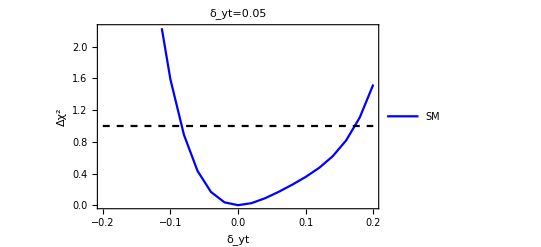

```mathematica
ListPlot[{intdytchi2en ,sig1},Joined->True,Frame->True,PlotStyle->{Blue,{Dashed,Black}},PlotLabel->Style["δ_yt=0.05",Black,20],PlotLegends->{"SM"},FrameLabel->{Style["δ_yt",Black,20],Style["Δχ^2",Black,15]},FrameTicksStyle->Directive[Black,13]]
```

```mathematica
(*bin angle and energy*)
sqrtback = Sqrt[background];
chi2 = Table[Sum[(signal[[i,j,k]]/ sqrtback[[i,j]])^2,{i,1,33},{j,2,17}],{k,1,Length@dytt}];
```

```mathematica
dytchi2enang = Table[{dytt[[k]],chi2 [[k]]},{k,1,Length@dytt}];
intdytchi2enang = Interpolation[dytchi2enang ]
sig1= Table[{dytt[[k]],1},{k,1,Length@dytt}];
```

InterpolatingFunction[…]

```mathematica
dyttnew = Table[(1/1000)*(i-200),{i,0,400}];
```

```mathematica
linear=Table[200.48908903408613dyttnew[[i]]^2,{i,1,401}];
```

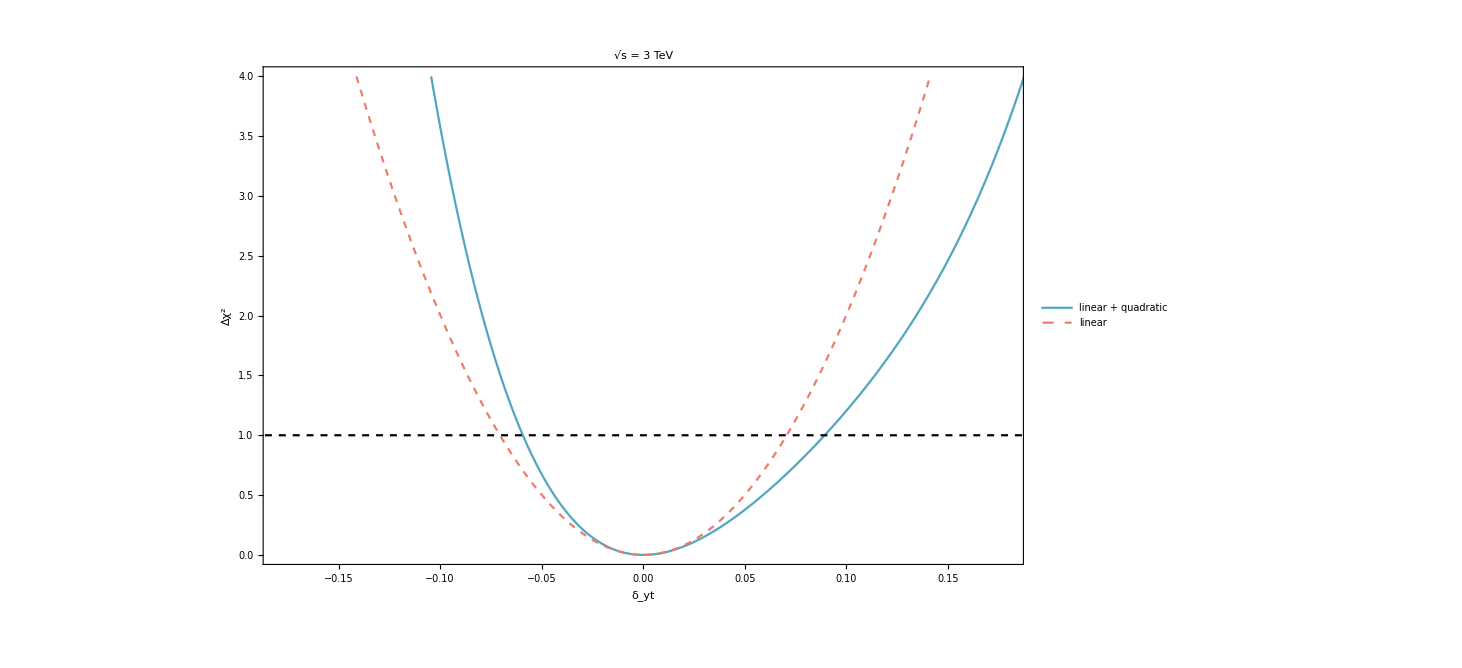

```mathematica
lineplot=ListPlot[{Transpose[{ dyttnew ,intdytchi2enang [dyttnew]}],sig1,Transpose[{ dyttnew ,linear}]},Joined->True,PlotStyle->{ColorData[colorselecitonumber][5],{Dashed,Black},{ColorData[colorselecitonumber][1],Dashed}},Frame->True,FrameLabel->{Style[DisplayForm["δ_yt"],Black,20,FontFamily->"Times"],Style["Δχ^2",Black,19,FontFamily->"Times"]},
PlotLabel->Style[DisplayForm[SqrtBox["s"] ]  Row[{" = ",3 TeV}]  ,Black,18,FontFamily->"Times"],
PlotLegends->Placed[LineLegend[{Directive[ColorData[colorselecitonumber][5]],Directive[ColorData[colorselecitonumber][1],Dashed]},{Style["linear + quadratic",FontFamily->"Times",15],Style["linear",FontFamily->"Times",15]}],{0.69,0.88}],
PlotRange->{{-0.18,0.18},{0,4}},
FrameTicksStyle->Directive[Black,17],ImageSize->500]
```

```mathematica
Export["chi_square_3TeV_angle_dilepton_out.pdf",lineplot]
```

chi_square_3TeV_angle_dilepton_out.pdf

```mathematica
data = Transpose[{ dyttnew ,intdytchi2enang [dyttnew]}];
```

```mathematica
a = Fit[data,{x^2,x^3,x^4},x]
```

200.489 x^2-1185.95 x^3+3856.15 x^4

```mathematica
(*

WW
222.07757435431694 -1160.7360243386208`+3129.950544729514

ZZ
2.8644397785039533 +10.108461304936863 +37.846172928965785 
ZZ+WW
200.48908903408613 -1185.9549144185619 +3856.145287341371 

2WW
887.9144252718696 - 9285.888194708981 +50079.20871567241
ZZ+2WW
841.8585046116536 - 9162.289863277603 + 52870.44916733302
*)
```

```mathematica
1160.7360243386208*8
```

9285.89

```mathematica
3129.950544729514*16
```

50079.2

```mathematica
3856.145287341371 -3129.950544729514-37.846172928965785
```

688.349

```mathematica
- 1185.9549144185619+1160.7360243386208-10.108461304936863
```

-35.3274

```mathematica
4*222.07757435431694 + 2*(200.48908903408613-222.07757435431694-2.8644397785039533)+2.8644397785039533
```

842.269

```mathematica
3129.950544729514*16 + 37.846172928965785 + 4 *688.348569682891
```

52870.4

```mathematica
-9162.289863277603 +8* 1160.7360243386208 - 10.108461304936863
```

113.49

```mathematica
(4*35.3274 + 113.49)/2
```

127.4

```mathematica
127.3998-35.327351384877915
```

92.0724

```mathematica
92*4  - 2*127
```

114

```mathematica
Clear[z]
```

```mathematica
200.48908903408613z^2 -1185.9549144185619 z^3 +3856.145287341371z^4//.z->.09
```

1.0124

```mathematica
(222.07757435431694z^2 -1160.7360243386208z^3+3129.950544729514z^4 )//. z-> -0.06
```

1.09076

```mathematica
200.48908903408613z^2 //.z->.07
```

0.982397